# Robocrystallographer Machine Learning

## Setup

## Packages

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[_, _]]//Once
```

## Directory

```mathematica
SetDirectory["C:\\Users\\sterg\\Documents\\GitHub\\sparks-baird\\ScabNet"]
```

C:\Users\sterg\Documents\GitHub\sparks-baird\ScabNet

```mathematica
{structureDir,materialsDir}=FileNameJoin@{"data",#}&/@{"structure_properties","materials_data"};
materialsProperty="stable_elasticity";
```

## Data

## Import

```mathematica
stableFeatures=Import[FileNameJoin@{structureDir,"stable_features.csv"},"Dataset",HeaderLines->1];
stableFeatures=stableFeatures⟦;;,3;;⟧;
```

```mathematica
{catNames,boolNames,floatNames}=Flatten@Import[FileNameJoin@{structureDir,#<>".csv"}]&/@{"cat_names","bool_names","float_names"};
```

```mathematica
{elasticTrain,elasticVal}=Import[FileNameJoin@{materialsDir,materialsProperty,#},"Dataset",HeaderLines->1]&/@{"train.csv","val.csv"};
```

## Reformat

```mathematica
stableNames=Keys@stableFeatures⟦1⟧;
targetNames={"energy","energy_per_atom","e_above_hull","formation_energy_per_atom"};
featureNames=catNames~Join~boolNames~Join~floatNames//Flatten;
```

```mathematica
{Subscript[mpids, robo],Subscript[X, robo]}=Normal@stableFeatures[;;,#]&/@{"task_id",featureNames};
rules=Thread[Subscript[mpids, robo]->Values@Subscript[X, robo]];
```

## Training and Validation Sets

```mathematica
{{Subscript[mpids, train],Subscript[K, VRH,train]},{Subscript[mpids, val],Subscript[K, VRH,val]}}=Table[Normal@i[;;,j],{i,{elasticTrain,elasticVal}},{j,{"task_id","target"}}];
{Subscript[X, train],Subscript[X, val]}=#/.rules&/@{Subscript[mpids, train],Subscript[mpids, val]};
```

### Fill Missing Data

Create an array with the correct datatypes for each feature in X_empty

```mathematica
Subscript[X, empty]=MapThread[ConstantArray[#1,Length@#2]&,{{"None",0.,False,0.},{catNames⟦;;2⟧,catNames⟦3;;3⟧,boolNames,floatNames}}]//Flatten;
```

Find positions of missing data

```mathematica
{Subscript[id, train],Subscript[id, val]}=Flatten@Position[#,_String,1]&/@{Subscript[X, train],Subscript[X, val]};
```

Replace missing data with X_empty

```mathematica
{Subscript[X, train],Subscript[X, val]}=MapThread[ReplacePart[#1,{#2}ᵀ->Subscript[X, empty]]&,{{Subscript[X, train],Subscript[X, val]},{Subscript[id, train],Subscript[id, val]}}];
```

## Prep data for Prediction

```mathematica
{train,val}=MapThread[Thread[#1->#2]&,{{Subscript[X, train],Subscript[X, val]},{Subscript[K, VRH,train],Subscript[K, VRH,val]}}];
```

## Machine Learning

## Dummy Predictor

```mathematica
Subscript[ℰ, dummy]=Mean@Abs[Subscript[K, VRH,train]-Mean@Subscript[K, VRH,train]]
```

56.7678

## Training

```mathematica
p=Predict[train,PerformanceGoal->"Quality",TargetDevice->"GPU"];
Information@%
```

Predictor information
Data type | Mixed (number: 156)
Standard deviation | 42.3 ± 1.5
Method | GradientBoostedTrees
Single evaluation time | 7.88 ms/example
Batch evaluation speed | 6.75 examples/ms
Loss | 5.18 ± 0.04
Model memory | 1.78 MB
Training examples used | 8693 examples
Training time | 18.6 s
 |

## Validation

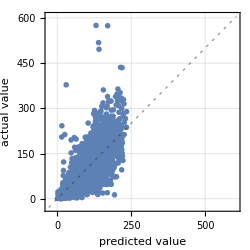
Predictor Measurements
Predictor method | GradientBoostedTrees
Number of test examples | 2485
Standard deviation | 46.5 ± 1.7
Standard deviation baseline | 72. ± 1.5
R-squared | 0.582 ± 0.035
Mean cross entropy | 5.28 ± 0.049
Single evaluation time | 12.1 ms/example
Batch evaluation speed | 847. examples/s
-Graphics- |

```mathematica
pm=PredictorMeasurements[p,val,ComputeUncertainty->True]
```

```mathematica
Subscript[ℰ, val]=pm["StandardDeviation"]
```

46.515

```mathematica
Subscript[ℰ, scaled]=Subscript[ℰ, val]/Subscript[ℰ, dummy]
```

0.81939

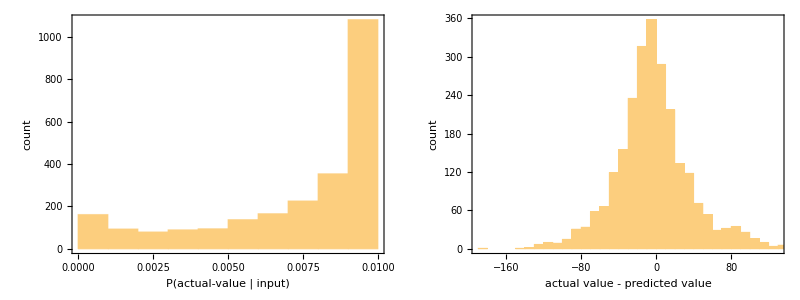

```mathematica
({pm[#]&/@{"ProbabilityDensityHistogram","ResidualHistogram"}})//TableForm
```

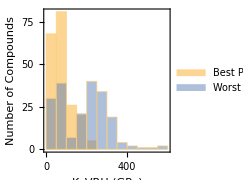

```mathematica
Histogram[Values@pm[#->200]&/@{"BestPredictedExamples","WorstPredictedExamples"},ChartLegends->Placed[Text@Style[#,10]&/@{"Best Predicted","Worst Predicted"},Above],Frame->True,FrameLabel->{"K_VRH (GPa)","Number of Compounds"},AspectRatio->1,ImageSize->Small]
```

# Code Graveyard

```mathematica
(*IntersectionPosition[s1_,s2_]:=({#,Position[s1,#]⟦1,1⟧,Position[s2,#]⟦1,1⟧}&/@Intersection[s1,s2])ᵀ*)
(*{values,pos1,pos2}=IntersectionPosition[Subscript[mpids, robo],Subscript[mpids, train]~Join~Subscript[mpids, val]];*)
```